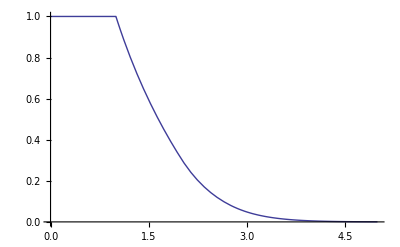
```mathematica
Dir="/home/mehdi/Documents/Mathematica/GNFS/04- Parallel";
SetDirectory[Dir];
PlotNo1=-Graphics-;
PlotNo2=-Graphics3D-;
PlotNo3=-Graphics3D-;
n=Input["Enter an integer number to factor:"];
DistributeDefinitions[n];
(*************Sieve Region************)
Maximuma=1;
Firstb=1;
Lastb=2;
(*********Factor Bases Bounds*********)
(*Rational Factor Base Upper Bound*)
RFBUpperBound=1;
(*Algebraic Factor Base Upper Bound*)
AFBUpperBound=1;
(*Quaderatic Character Base Size*)
QCBSize=50;
RFB={};
AFB={};
QCB={};
AFBSize=1;
RFBSize=1;
d=3;
LinearPolyLNorm=0;
CP={};
Res={};
factor={};
Off[OpenRead::"noopen",Power::"indet",Needs::"nocont",InterpolatingFunction::"dmval", FunctionInterpolation::"ncvb"];
(*********Load and Save each step calculation results***********)
Loadstatus[size_]:=Module[{fname,s,Var,l,i,stp=0,cmd},
fname=FileNameJoin[{Dir,(ToString[n]<>size<>".txt")}];
s=OpenRead[fname];
If[s==$Failed,Return[0];];
Var=ReadList[s];
Close[s];
If[Length[Var]<1,Return[0];];
Var=Flatten[Var,1];
stp=Var[[1,2]];
l=Length[Var];
For[i=2,i≤l,i++,
cmd=Var[[i,1]]<>"="<>ToString[Var[[i,2]]]<>";";
ToExpression[cmd];
];
DistributeDefinitions[n,m,CP,Maximuma,Lastb,Firstb,d,AFBUpperBound];
If[stp>1,
BasisSize=RFBSize+AFBSize+QCBSize;
DistributeDefinitions[RFBSize,RFB,AFBSize,AFB];
];
f[x_]:=∑_(k=1)^(k=(d+1)) (CP[[k]]*x^(d+1-k));
F[x_,y_]:=((-y)^d)*f[-x/y];
Return[stp];
];
SaveStatus[n_,Stp_,size_]:=Module[{Var={},Tmp={},fname,s},
Tmp={"Step",Stp};
AppendTo[Var,Tmp];
Tmp={"n",n};
AppendTo[Var,Tmp];
Tmp={"d",d};
AppendTo[Var,Tmp];
Tmp={"RFBUpperBound",RFBUpperBound};
AppendTo[Var,Tmp];
Tmp={"AFBUpperBound",AFBUpperBound};
AppendTo[Var,Tmp];
Tmp={"Maximuma",Maximuma};
AppendTo[Var,Tmp];
Tmp={"Lastb",Lastb};
AppendTo[Var,Tmp];
If[Stp>0,
Tmp={"m",m};
AppendTo[Var,Tmp];
Tmp={"CP",CP};
AppendTo[Var,Tmp];
];
If[Stp>1,
Tmp={"RFBSize",RFBSize};
AppendTo[Var,Tmp];
Tmp={"RFB",RFB};
AppendTo[Var,Tmp];
Tmp={"AFBSize",AFBSize};
AppendTo[Var,Tmp];
Tmp={"AFB",AFB};
AppendTo[Var,Tmp];
Tmp={"QCBSize",QCBSize};
AppendTo[Var,Tmp];
Tmp={"QCB",QCB};
AppendTo[Var,Tmp];
];
If[Stp>2,
Tmp={"Res",Res};
AppendTo[Var,Tmp];
Tmp={"NumberOfRelations",NumberOfRelations};
AppendTo[Var,Tmp];
];
fname=FileNameJoin[{Dir,(ToString[n]<>size<>".txt")}];
s=OpenWrite[fname];
Write[s,Var];
Close[s];
];
(************Computing Bounds*************)
AsymptoticBound[n_,d_,o1_]:=Exp[(1/2+o1)(d Log[d]+√((d (Log[d])^2+2/d Log[n]*Log[Log[n]/d])))];
CalcBounds[n_,size_]:=Module[{c1,c2,c3,c4,c5},
If[size== "s",c1=1/125;c2=1/9;c3=1/4;c4=3;c5=0;];
If[size== "m",c1=1/60;c2=1/9;c3=3/10;c4=5/2;c5=0;];
If[size== "l",c1=1/50;c2=2/17;c3=1/3;c4=2;c5=0.1;];
If[size== "xl",c1=1/100;c2=1/9;c3=1/4;c4=3;c5=1;];
If[size== "h",c1=1/45;c2=1/8;c3=5/12;c4=5/2;c5=1;];
d=Round[(3^(1/3)+1/7)×(Log[n]/(2Log[Log[n]]))^(1/3)+c5];
RFBUpperBound=IntegerPart[AsymptoticBound[n,d,c1]];
AFBUpperBound=IntegerPart[AsymptoticBound[n,d,c2]];
Maximuma=IntegerPart[AsymptoticBound[n,d,c3]];
Lastb=IntegerPart[Maximuma/c4];
DistributeDefinitions[Maximuma,Lastb,Firstb,d,AFBUpperBound];
];
(*******Polynomial Selection*******)
PolyLNorm[P_,d_,afbu_]:=Module[{p,Fp,cntr,cntF,nrmF=0,l,r,x1,afbt},
p=2;
Fp[x_,y_]:=((-y)^d)*P[-x/y];
afbt=Min[afbu,100];
While[p≤afbt,
r=x1/.Solve[Reduce[P[x1]==0,{x1},Modulus->p]];
l=Length[r];
cntr=1/(p-1);
cntF=l p/(p^2-1);
nrmF+=(cntr-cntF)*Log[p];
p=NextPrime[p];
];
Return[nrmF];
];
SelectMonicPolynomial[n_,d_,afbu_]:=Module[{P,i,tmpM,tmpα=3,PNorm,coef,Ml,Mu},
Mu=Floor[n^(1/d)];
Ml=Ceiling[(n/2)^(1/d)];
For[i=Ml,i≤ Mu,i++,
tmpM=i;
coef=IntegerDigits[n,tmpM,(d+1)];
P[x_]:=∑_(k=1)^(k=(d+1)) (coef[[k]]*x^(d+1-k));
PNorm=PolyLNorm[P,d,afbu];
If[PNorm≤tmpα,
tmpα=PNorm;
CP=coef;
m=tmpM;
];
];
f[x_]:=∑_(k=1)^(k=(d+1)) (CP[[k]]*x^(d+1-k));
F[x_,y_]:=((-y)^d)*f[-x/y];
Return[{(Mu-Ml+1),tmpα}];
];
(*******Polynomial Selection Parallel*******)
SelectMonicPolynomialParallel[intrv_]:=Module[{P,i,tmpM,tmpα=3,PNorm,coef,Ml,Mu,Mld,Mup,CPloc,mloc,l},
Mu=Floor[n^(1/d)];
Ml=Ceiling[(n/2)^(1/d)];
l=(Mu-Ml)/$ProcessorCount;
Mld=Floor[Ml+(intrv-1)l];
Mup=Ceiling[Ml+intrv*l];
For[i=Mld,i≤ Mup,i++,
tmpM=i;
coef=IntegerDigits[n,tmpM,(d+1)];
P[x_]:=∑_(k=1)^(k=(d+1)) (coef[[k]]*x^(d+1-k));
PNorm=PolyLNorm[P,d,AFBUpperBound];
If[PNorm≤tmpα,
tmpα=PNorm;
CPloc=coef;
mloc=tmpM;
];
];
Return[{(CPloc),mloc,N[tmpα]}];
];
ParallelSelPol[]:=Module[{NumCPU,TMP,tmpα=3,i,iSel=0},
NumCPU=$ProcessorCount;
TMP=Parallelize[Table[SelectMonicPolynomialParallel[i],{i,1,NumCPU}]];
For[i=1,i≤NumCPU,i++,
If[TMP[[i,3]]<tmpα,
tmpα=TMP[[i,3]];
iSel=i;
];
];
m=TMP[[iSel,2]];
CP=TMP[[iSel,1]];
DistributeDefinitions[m,CP];
f[x_]:=∑_(k=1)^(k=(d+1)) (CP[[k]]*x^(d+1-k));
F[x_,y_]:=((-y)^d)*f[-x/y];
Return[{Ceiling[(1-(1/2)^(1/d))n^(1/d)],tmpα}];
];
(*******Test Selected Polynimial for Irreduceablity******)
ChkPlyIrr[P_]:=Module[{Lst,fct,Nfct,PsblFct={}},
Lst=FactorList[P[x]];
Nfct=Length[Lst];
If[Nfct== 2,Return[{}],
For[fct=2,fct≤ Nfct,fct++,
AppendTo[PsblFct,(Lst[[fct,1]]/.x->m)];
];
];
Return[PsblFct];
];
(**********Generating RFB**********)
GenerateRFB[]:=Module[{TmpRFB={},urfb=RFBUpperBound,p,randP,cntr,cntG},
p=2;
While[p≤urfb,
cntr=1/(p-1);
cntG=p/(p^2-1);
LinearPolyLNorm+=(cntr-cntG)*Log[p];
AppendTo[TmpRFB,p];
p=NextPrime[p];
];
randP=RandomPrime[{urfb,IntegerPart[urfb^(3/2)]}];
AppendTo[TmpRFB,randP];
RFB=TmpRFB;
RFBSize=Length[RFB];
DistributeDefinitions[RFB,RFBSize];
];
(**********Generating AFB***********)
GenerateAFB[]:=Module[{TmpAFB={},uafb=AFBUpperBound,p,x,r,l,i,randP},
p=2;
While[p≤uafb,
r=x/.Solve[Reduce[f[x]==0,{x},Modulus->p]];
l=Length[r];
If[l>0,
For[i=1,i≤l,i++,
AppendTo[TmpAFB,{p,r[[i]]}];
];
];
p=NextPrime[p];
];
l=0;
While[l==0,
randP=RandomPrime[{uafb,IntegerPart[uafb^(4/3)]}];
r=x/.Solve[Reduce[f[x]==0,{x},Modulus->randP]];
l=Length[r];
If[l>0,
For[i=1,i≤l,i++,
AppendTo[TmpAFB,{randP,r[[i]]}];
];
];
];
AFB=TmpAFB;
AFBSize=Length[AFB];
DistributeDefinitions[AFB,AFBSize];
];
(********Generating QCB**********)
GenerateQCB[]:=Module[{TmpQCB={},uafb=AFBUpperBound,s,p,x,r,i=1,j,l},
p=NextPrime[uafb];
While[i≤QCBSize,
r=x/.Solve[Reduce[f[x]==0,{x},Modulus->p]];
l=Length[r];
If[l>0,
For[j=1,j≤l,j++,
s=r[[j]];
If[Mod[f'[s],p]≠0,
AppendTo[TmpQCB,{p,s}];
i++;
];
];
];
p=NextPrime[p];
];
QCB=TmpQCB;
Return[TmpQCB];
];
(************************Smoonthness Over Basis***************************)
SmoothOverAFB[a_,b_]:=Module[{Nrm,L,p,r,i,exp},
Off[Power::"indet"];
Nrm=F[a,b];
L=AFBSize;
For[i=1,i≤L,i++,
p=AFB[[i,1]];
r=AFB[[i,2]];
If[(Nrm≠0)&&(Mod[a+b*r,p]==0),
exp=IntegerExponent[Nrm,p];
If[exp≠0,
Nrm=Nrm/p^exp;
];
];
If[Abs[Nrm]==1,Return[True]];
];
If[Abs[Nrm]==1,
Return[True];
,
Return[False];
];
];
SmoothOverRFB[a_,b_]:=Module[{tmp,L,p,i,exp},
tmp=a+b m;
L=RFBSize;
For[i=1,i≤L,i++,
p=RFB[[i]];
If[(tmp≠0)&&(Mod[tmp,p]==0),
exp=IntegerExponent[tmp,p];
If[exp≠0,
tmp=tmp/p^exp;
];
];
If[Abs[tmp]==1,Return[True]];
];
If[Abs[tmp]==1,
Return[True];
,
Return[False];
];
];
(************************Linear Sieve***************************)
LinearSieveRegion[Mina_,Maxa_,Minb_,Maxb_]:=Module[{a,b,Relations={}},
For[b=Minb,b≤Maxb,b++,
For[a=Mina,a≤Maxa,a++,
If[(Abs[GCD[a,b]]==1),
If[SmoothOverAFB[a,b],
If[SmoothOverRFB[a,b],
AppendTo[Relations,{a,b}];
];
];
];
];
];
Return[Relations];
];
(**************************Parallel Linear Sieve**************************)
SieveOnKernels[c_]:=Module[{intLength,NumCPU,Rs},
NumCPU=$ProcessorCount;
intLength=2Maximuma/NumCPU;
Rs=LinearSieveRegion[(-Maximuma+(c-1)intLength),(-Maximuma+c*intLength),Firstb,Lastb];
Return[Rs];
];
ParallelSieve[]:=Module[{NumCPU,TMP,Rels={},i},
NumCPU=$ProcessorCount;
TMP=Parallelize[Table[SieveOnKernels[i],{i,1,NumCPU}]];
For[i=1,i≤NumCPU,i++,
Rels=Union[Rels,TMP[[i]]];
];
Return[Rels];
];
(************Constructing the matrix of power vectors and Quaderatic Characters************)
BuildMatrix[Sieve_]:=Module[{M={},l1,l2,l3,l4,a,b,p,r,i,j,mix,exp,tmp},
l1=Length[Sieve];
l2=Length[RFB];
l3=Length[AFB];
l4=Length[QCB];
For[i=1,i≤l1,i++,
tmp={};
a=Sieve[[i,1]];
b=Sieve[[i,2]];
mix=a+m*b;
If[mix<0,AppendTo[tmp,1],AppendTo[tmp,0]];
For[j=1,j≤l2,j++,
p=RFB[[j]];
exp=IntegerExponent[mix,p];
AppendTo[tmp,Mod[exp,2]];
];
For[j=1,j≤l3,j++,
p=AFB[[j,1]];
r=AFB[[j,2]];
mix=F[a,b];
If[Mod[a+r*b,p]==0,
exp=IntegerExponent[mix,p];
,exp=0;
];
AppendTo[tmp,Mod[exp,2]];
];
For[j=1,j≤l4,j++,
p=QCB[[j,1]];
r=QCB[[j,2]];
mix=a+p*b;
If[JacobiSymbol[(a+r*b),p]==1,exp=0,exp=1];
AppendTo[tmp,exp];
];
tmp=Flatten[tmp];
AppendTo[M,tmp];
];
Return[M];
];
(*****************Finding Square roots on Z and ϕ(Z[θ])*****************)
FindSquares[Sieve_,A_]:=Module[{a,b,i,l,α=1,θ,x1=0,x2,Y,tmp=1,f1,f2,β,tmpPairs={}},
l=Length[A];
θ=AlgebraicNumber[Root[f[x],x,1],{0,1}];
For[i=1,i≤l,i++,
If[A[[i]]≠0,
a=Sieve[[i,1]];
b=Sieve[[i,2]];
AppendTo[tmpPairs,{a,b}];
α=α*AlgebraicNumber[θ,{a,b}];
tmp=tmp*(a+m*b);
];
];
α=α*(f'[θ])*(f'[θ]);
Quiet[β=ToNumberField[Sqrt[α],θ];];
Quiet[Y=β[[2]]];
For[i=1,i≤Length[Y],i++,
x1=Mod[(x1+Mod[m^(i-1)*Y[[i]],n]),n];
];
x2=Sqrt[tmp];
Return[{x1,x2}];
];
(***********Check resulted squares for a appropriate factor***********)
CheckSquares[S_]:=Module[{f1,f2},
f1=GCD[(S[[1]]-S[[2]]),n];
If[(f1<n) && (f1>1),
Return[f1];
];
f2=GCD[(S[[1]]+S[[2]]),n];
If[(f2<n) && (f2>1),
Return[f2];
];
Return[0];
];
(**********Constructing Dependency Space**********)
DependencySpace[M_]:=Module[{Nu},
Nu=NullSpace[Transpose[M],Modulus->2];
Return[Nu];
];
(***********Searching for a good dependency***********)
ScanningNullSpace[N_,SieveRes_]:=Module[{Rnk,k,sqrs,fact=0,idx,jdx,WholeSet,SubSet,j,DepVec,NullVector},
Rnk=Length[N];
NullVector=Table[0,{i,1,NumberOfRelations}];
For[k=1,k≤Rnk,k++,
Print[Panel[StringForm["Scanning Linear combinations of length ``",k]]];
WholeSet=Table[i,{i,1,Rnk}];
idx=k;
While[idx>0,
DepVec=NullVector;
SubSet=Table[WholeSet[[i]],{i,1,k}];
For[j=1,j≤k,j++,
DepVec=DepVec+N[[SubSet[[j]]]];
];
sqrs=FindSquares[SieveRes,DepVec];
fact=CheckSquares[sqrs];
If[fact≠0,Return[fact];];
idx=k;
While[(idx>0)&&(WholeSet[[idx]]==(Rnk-k+idx)),idx--;];
If[idx>0,
WholeSet[[idx]]=WholeSet[[idx]]+1;
For[jdx=(idx+1),jdx≤Rnk,jdx++,
WholeSet[[jdx]]=WholeSet[[jdx-1]]+1;
];
];
];
];
Return[fact];
];
(*******************Parallel Scanning*******************)
ScanningNullSpacePart[Par_]:=Module[{c,N,SieveRes,NumCPU,Rnk,k,sqrs,fact=0,idx,jdx,WholeSet,SubSet,j,DepVec,NullVector,to,SubSpaceRnk},
c=Par[[1]];
N=Par[[2]];
SieveRes=Par[[3]];
NumCPU=$ProcessorCount;
Rnk=Length[N];
to=Floor[Rnk/NumCPU];
NullVector=Table[0,{i,1,NumberOfRelations}];
For[k=0,k≤to,k++,
SubSpaceRnk=k*NumCPU+c;
If[SubSpaceRnk≤Rnk,
Print[Panel[StringForm["Scanning Linear combinations of length ``",SubSpaceRnk]]];
WholeSet=Table[i,{i,1,Rnk}];
idx=SubSpaceRnk;
While[idx>0,
DepVec=NullVector;
SubSet=Table[WholeSet[[i]],{i,1,SubSpaceRnk}];
For[j=1,j≤SubSpaceRnk,j++,
DepVec=DepVec+N[[SubSet[[j]]]];
];
sqrs=FindSquares[SieveRes,DepVec];
fact=CheckSquares[sqrs];
If[fact≠0,Return[fact];];
idx=SubSpaceRnk;
While[(idx>0)&&(WholeSet[[idx]]==(Rnk-SubSpaceRnk+idx)),idx--;];
If[idx>0,
WholeSet[[idx]]=WholeSet[[idx]]+1;
For[jdx=(idx+1),jdx≤Rnk,jdx++,
WholeSet[[jdx]]=WholeSet[[jdx-1]]+1;
];
];
];
];
];
Return[fact];
];
ParallelScanNullSpace[N_,Res_]:=Module[{NumCPU,TMP,Rels={},i},
NumCPU=$ProcessorCount;
(*TMP=Parallelize[Table[ScanningNullSpacePart[i,N,Res],{i,1,NumCPU}]];*)
TMP=ParallelTry[ScanningNullSpacePart,Table[{i,N,Res},{i,1,NumCPU}]];
Return[TMP];
];
(**************************GNFS*************************)
GNFS[n_,size_]:=Module[{ParamTab,TPS,Init,PolynomialStep,ChkPly,Res,M,NS,ResTab,scale},
If[PrimeQ[n],
isPrime=True;
ParamTab=StringForm["`` is prime.",n];
Facts="Nothing to factor.";
Print[Panel[ ParamTab]]
,
isPrime=False;
CalcBounds[n,size];
GenerateRFB[];
TPS=AbsoluteTiming[PolynomialStep=SelectMonicPolynomial[n,d,AFBUpperBound];];
Init=StringForm["Suggested Algebraic Factor Base bound: ``\nSuggested Rational Factor Base bound: ``\nNumber of sieved polynomials: ``\nMin(α(F))=``\n[Using Murphy's method for monic polynomials]",AFBUpperBound,RFBUpperBound,PolynomialStep[[1]],N[PolynomialStep[[2]]]];
Print[TabView[{"Initialization"->Init,"Running time"->StringForm["`` Seconds.",N[TPS[[1]]]]}]];
GenerateAFB[];
GenerateQCB[];
BasisSize=RFBSize+AFBSize+Length[QCB];
scale=Switch[size,"s","Small","m","Medium","l","Large","xl","Extra Large","h","Huge"];
ParamTab=StringForm["The number to be factor: ``\nm=``\nf(x)=``\nUsing `` scales.\n|RFB|+|AFB|+|QCB|=``+``+``=``\nSieve Region: [``,``]×[``,``]",n,m,f[x],scale,RFBSize,AFBSize,Length[QCB],BasisSize,-Maximuma,Maximuma,Firstb,Lastb];
Print[TabView[{"Parameters"->ParamTab,"RFB"->RFB,"AFB"->AFB,"QCB"->QCB,"ρ(u)"-> PlotNo1,"σ(u,v)"-> PlotNo2,"ρ(u)+σ(u,v)"-> PlotNo3}]];
ChkPly=ChkPlyIrr[f];
If[Length[ChkPly]>0,
factor=ChkPly;
,
Res=LinearSieveRegion[-Maximuma,Maximuma,Firstb,Lastb];
NumberOfRelations=Length[Res];
M=BuildMatrix[Res];
NS=DependencySpace[M];
ResTab=StringForm["Number of Relation on sieve region: ``\nMatrix Dimensions: ``\nDimension of Null Space: ``",NumberOfRelations,Dimensions[M],Length[NS]];
Print[Panel[ ResTab]];
AppendTo[factor,ScanningNullSpace[NS,Res]];
];
];
Return[factor];
];
(**************************GNFS Parallel*************************)
GNFSParallel[n_,size_]:=Module[{ParamTab,TPS,Init,PolynomialStep,ChkPly,Res,M,NS,ResTab,scale},
If[PrimeQ[n],
isPrime=True;
ParamTab=StringForm["`` is prime.",n];
Facts="Nothing to factor.";
Print[Panel[ ParamTab]]
,
isPrime=False;
CalcBounds[n,size];
GenerateRFB[];
DistributeDefinitions[PolyLNorm,SelectMonicPolynomialParallel];
TPS=AbsoluteTiming[PolynomialStep=ParallelSelPol[];];
Init=StringForm["Suggested Algebraic Factor Base bound: ``\nSuggested Rational Factor Base bound: ``\nNumber of sieved polynomials: ``\nMin(α(F))=``\n[Using Murphy's method for monic polynomials]",AFBUpperBound,RFBUpperBound,PolynomialStep[[1]],N[PolynomialStep[[2]]]];
Print[TabView[{"Initialization"->Init,"System Info"->StringForm["Available Cpu(s): ``\nOS: ``",$ProcessorCount,$System],"Running time"->StringForm["`` Seconds.",N[TPS[[1]]]]}]];
GenerateAFB[];
GenerateQCB[];
BasisSize=RFBSize+AFBSize+Length[QCB];
scale=Switch[size,"s","Small","m","Medium","l","Large","xl","Extra Large","h","Huge"];
ParamTab=StringForm["The number to be factor: ``\nm=``\nf(x)=``\nUsing `` scales.\n|RFB|+|AFB|+|QCB|=``+``+``=``\nSieve Region: [``,``]×[``,``]",n,m,f[x],scale,RFBSize,AFBSize,Length[QCB],BasisSize,-Maximuma,Maximuma,Firstb,Lastb];
Print[TabView[{"Parameters"->ParamTab,"RFB"->RFB,"AFB"->AFB,"QCB"->QCB,"ρ(u)"->PlotNo1,"σ(u,v)"-> PlotNo2,"ρ(u)+σ(u,v)"-> PlotNo3}]];
ChkPly=ChkPlyIrr[f];
If[Length[ChkPly]>0,
factor=ChkPly;
,
DistributeDefinitions[f,F,SmoothOverAFB,SmoothOverRFB, LinearSieveRegion,SieveOnKernels];
Res=ParallelSieve[];
NumberOfRelations=Length[Res];
M=BuildMatrix[Res];
NS=DependencySpace[M];
ResTab=StringForm["Number of Relation on sieve region: ``\nMatrix Dimensions: ``\nDimension of Null Space: ``",NumberOfRelations,Dimensions[M],Length[NS]];
Print[Panel[ ResTab]];
DistributeDefinitions[NumberOfRelations,FindSquares,CheckSquares,ScanningNullSpacePart];
AppendTo[factor,ParallelScanNullSpace[NS,Res]];
];
];
Return[factor];
];
(***********************GNFS Parallel Save & Load Data**********************)
GNFSParallelIO[n_,size_]:=Module[{ParamTab,TPS,Init,PolynomialStep,ChkPly,M,NS,ResTab,scale,loadstep},
If[PrimeQ[n],
isPrime=True;
ParamTab=StringForm["`` is prime.",n];
Facts="Nothing to factor.";
Print[Panel[ ParamTab]]
,
isPrime=False;
loadstep=Loadstatus[size];
If[loadstep<1,
CalcBounds[n,size];
GenerateRFB[];
DistributeDefinitions[PolyLNorm,SelectMonicPolynomialParallel];
TPS=AbsoluteTiming[PolynomialStep=ParallelSelPol[];];
SaveStatus[n,1,size];
Init=StringForm["Suggested Algebraic Factor Base bound: ``\nSuggested Rational Factor Base bound: ``\nNumber of sieved polynomials: ``\nMin(α(F))=``\n[Using Murphy's method for monic polynomials]",AFBUpperBound,RFBUpperBound,PolynomialStep[[1]],N[PolynomialStep[[2]]]];
Print[TabView[{"Initialization"->Init,"System Info"->StringForm["Available Cpu(s): ``\nOS: ``",$ProcessorCount,$System],"Running time"->StringForm["`` Seconds.",N[TPS[[1]]]]}]];
];
If[loadstep<2,
GenerateAFB[];
GenerateQCB[];
BasisSize=RFBSize+AFBSize+Length[QCB];
SaveStatus[n,2,size];
scale=Switch[size,"s","Small","m","Medium","l","Large","xl","Extra Large","h","Huge"];
ParamTab=StringForm["The number to be factor: ``\nm=``\nf(x)=``\nUsing `` scales.\n|RFB|+|AFB|+|QCB|=``+``+``=``\nSieve Region: [``,``]×[``,``]",n,m,f[x],scale,RFBSize,AFBSize,Length[QCB],BasisSize,-Maximuma,Maximuma,Firstb,Lastb];
Print[TabView[{"Parameters"->ParamTab,"RFB"->RFB,"AFB"->AFB,"QCB"->QCB,"ρ(u)"-> PlotNo1,"σ(u,v)"-> PlotNo2,"ρ(u)+σ(u,v)"-> PlotNo3}]];
];
ChkPly=ChkPlyIrr[f];
If[Length[ChkPly]>0,
factor=ChkPly;
,
If[loadstep<3,
DistributeDefinitions[f,F,SmoothOverAFB,SmoothOverRFB, LinearSieveRegion,SieveOnKernels];
Res=ParallelSieve[];
NumberOfRelations=Length[Res];
SaveStatus[n,3,size];
];
M=BuildMatrix[Res];
NS=DependencySpace[M];
ResTab=StringForm["Number of Relation on sieve region: ``\nMatrix Dimensions: ``\nDimension of Null Space: ``",NumberOfRelations,Dimensions[M],Length[NS]];
Print[Panel[ ResTab]];
DistributeDefinitions[NumberOfRelations,FindSquares,CheckSquares,ScanningNullSpacePart];
AppendTo[factor,ParallelScanNullSpace[NS,Res]];
];
];
Return[factor];
];
(********************Full Process Parallel***********************)
ProcessGNFS[n_,size_,mod_]:=Module[{T,Facts,RunTime},
If[mod=="Simple",
T=AbsoluteTiming[
GNFS[n,size];
];
];

If[mod=="Parallel",
T=AbsoluteTiming[
GNFSParallel[n,size];
];
];
If[mod=="PIO",
T=AbsoluteTiming[
GNFSParallelIO[n,size];
];
];
If[Length[factor]==0,
Facts=StringForm["No factor find!\nComplete Factorization: ``",FactorInteger[n]];,
Facts=StringForm["Find factor(s): ``\nComplete Factorization: ``",factor,FactorInteger[n]];
];
RunTime=StringForm["Total running time: `` seconds.",N[T[[1]]]];
If[!isPrime,
Print[TabView[{"GNFS results"-> Facts,"Running Time"->RunTime}]];
];
];
(*************************Usage*******************************)
ProcessGNFS[n,"l","PIO"];
(***************************Results*******************************)
```

123

1234567

Number of Relation on sieve region: 116
Matrix Dimensions: {116, 83}
Dimension of Null Space: 81

Scanning Linear combinations of length 1

Scanning Linear combinations of length 2

12